```mathematica
init:=(
δt=0.01;
f=v=r=0;
fluidDensity=1;
gravity=-9.81;
);
step[radius_,density_]:=(
(*Buoyancy*)
With[{volume=4/3 π radius^3},
f+=(fluidDensity-density)*volume;
f+=gravity*volume*density;
];
(*Integrate*)
v +=f*δt;
r +=v*δt;
f=0;
v*=0.97;
r
);
```

```mathematica
trajectory[radius_,density_]:=(init;Table[step[radius,density],50]);
```

```mathematica
trajectory[1,1]
```

{-0.0041092,-0.0122043,-0.0241658,-0.0398777,-0.0592273,-0.0821057,-0.108407,-0.138028,-0.17087,-0.206836,-0.245832,-0.287768,-0.332555,-0.380107,-0.430342,-0.483179,-0.53854,-0.596349,-0.656534,-0.719022,-0.783744,-0.850634,-0.919627,-0.990659,-1.06367,-1.1386,-1.21539,-1.29399,-1.37433,-1.45638,-1.54007,-1.62536,-1.71221,-1.80055,-1.89036,-1.98158,-2.07417,-2.1681,-2.26331,-2.35978,-2.45747,-2.55633,-2.65633,-2.75745,-2.85964,-2.96287,-3.06712,-3.17235,-3.27853,-3.38563}

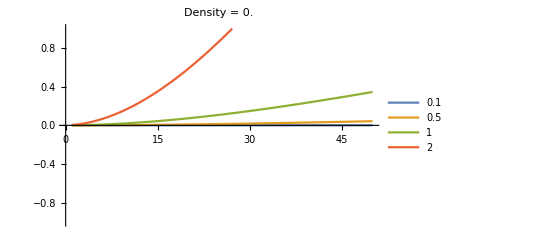
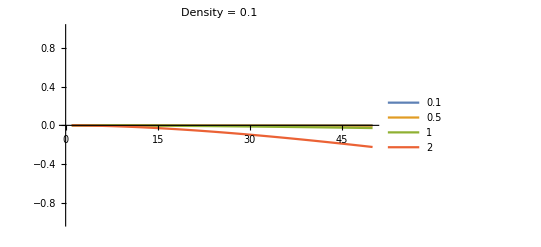
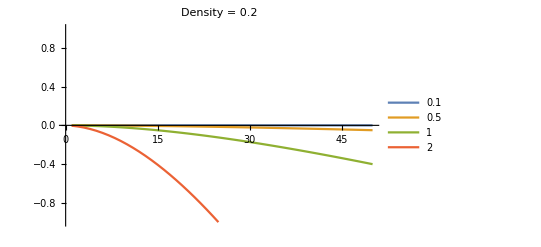
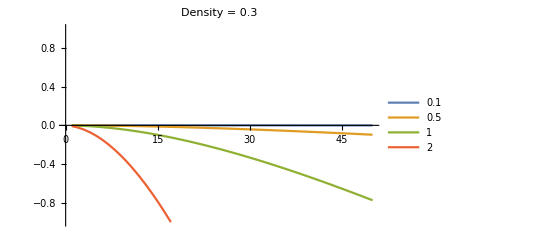
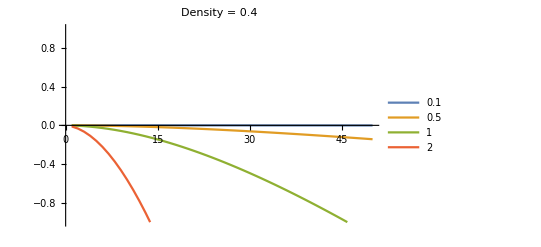
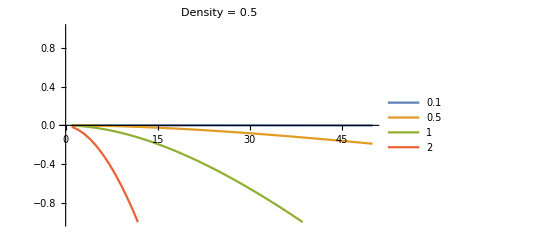
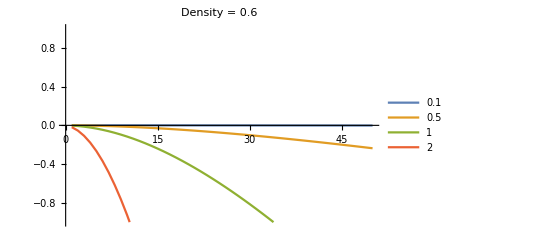
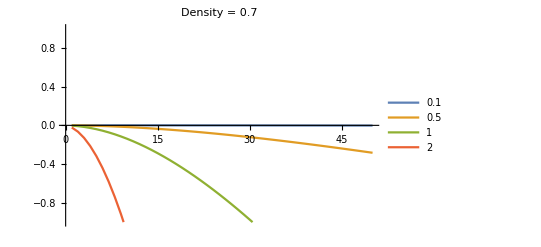

```mathematica
Table[
With[{rads={0.1,0.5,1,2}},
ListLinePlot[trajectory[#,density]&/@rads,PlotLegends->rads,PlotLabel->StringForm["Density = ``",density],PlotRange->{-1,1}]],{density,0,2 fluidDensity,0.1}]
```

```mathematica
ListPlot3D[Table[trajectory[#,density],{density,0,2*fluidDensity}]&/@{0.1,1,2*fluidDensity},AxesLabel->{"time","density","distance"},PlotLegends->{0.1,1,2}]
```

-Graphics3D-